# QMeSTools Showcase

## Load Package

```mathematica
(* Load the installed version of the package *)
Needs["QMeSderivation`"]
```

## Define the theory (a QCD truncation)

```mathematica
fRGEq = {
"Prefactor"->{1/2},
<|"type"->"Regulatordot", "indices"->{i,j}|>,
<|"type"->"Propagator", "indices"->{i,j}|>
};

fieldsQCD=<|
"bosonic"-> {
σ[p],(*sigma meson*)
Π[p,{a}],(*pions*)
 A[p,{v, c}](*gluon*)
},
 "fermionic"->{
{sb[p,{d,c}],s[p,{d,c}]},(*strange quark*)
{qb[p,{d,c,f}],q[p,{d,c,f}]},(*light quarks*)
{cb[p,{c}],c[p,{c}]}(*ghosts*)
}
|>;

TruncationQCD = {
{σ,σ},{Π,Π},{q,qb},{s,sb},{A,A},{c,cb},(* propagators *)
{qb,q,A},{cb,c,A},{sb,s,A},{A,A,A},{A,A,A,A},(* gluon sector scatterings *)
{qb,q,σ},{qb,q,Π},{qb,q,σ,σ},{qb,q,Π,Π},{qb,q,σ,Π},{qb,q,σ,σ,σ},{qb,q,σ,σ,Π},{qb,q,σ,Π,Π},{qb,q,Π,Π,Π}, (* quark-meson scatterings *)
 {σ,σ,σ},{σ,Π,Π},{σ,σ,σ,σ},{σ,σ,Π,Π},{Π,Π,Π,Π}(* meson scatterings *)
};

SetupfRGQCD= <|"MasterEquation"->fRGEq,
"FieldSpace"->fieldsQCD,
"Truncation"->TruncationQCD
|>;
```

## FRG Equations: Four-Quark vertex

### Derive flow equation of four-quark vertex

```mathematica
DerivativeListqbqqbq= {qb[p,{d4,c4,f4}],q[-p,{d3,c3,f3}],qb[p,{d2,c2,f2}],q[-p,{d1,c1,f1}]};
Diagramsqbqqbq=DeriveFunctionalEquation[SetupfRGQCD,DerivativeListqbqqbq,"OutputLevel"->"SuperindexDiagrams"];
Diagramsqbqqbq//Length
```

400

### Reduce the number of diagrams by using the symmetries of the tensor structure and the t-channel configuration

```mathematica
ReduceIdenticalFlowDiagrams::usage
```

ReduceIdenticalFlowDiagrams[diagrams,derivativeList,symmetries]

Reduce a set of flow equations by matching identical topologies and/or by utilizing a given set of symmetries.
The user has to supply the list of derivatives (i.e. external legs in the diagrams). Then, the symmetries are specified in the following way:
symmetries = {
	{ {1, 3}, Minus},
	{ {2, 4}, Minus}
	{ {1, 3}, {2, 4}, Plus},
}
Here, two antisymmetries (as specified by the Minus) are given, which consist of a single cycle each (1,3) and (2,4). These integers refer to the legs as given in derivativeList (in order).
ReduceIdenticalFlowDiagrams does not construct all symmetries from the given ones - therefore, the full symmetry group needs to be specified. Therefore, we also supply the symmetry consisting of both cycles explicitly in the third line.

```mathematica
symmetries={
{{1,3},Plus},
{{2,4},Plus},
{{1,3},{2,4},Plus}
};
DiagramsqbqqbqReduced=ReduceIdenticalFlowDiagrams[Diagramsqbqqbq,DerivativeListqbqqbq,symmetries];
DiagramsqbqqbqReduced//Length
```

61

### Plot the resulting diagrams

```mathematica
PlotSuperindexDiagram::usage
```

PlotSuperindexDiagram[diagram, setup, options]

Plot one or multiple superindex diagrams. The first argument to this function are the diagram(s), the second one is the corresponding QMeS setup.
The diagram(s) have to be superindex diagram(s).

The options for the function PlotSuperindexDiagram are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.

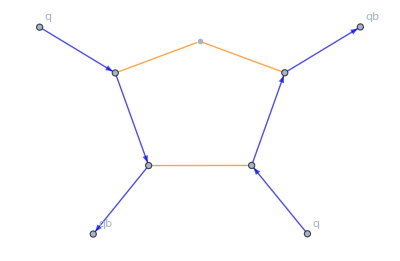
{4,-Graphics-}

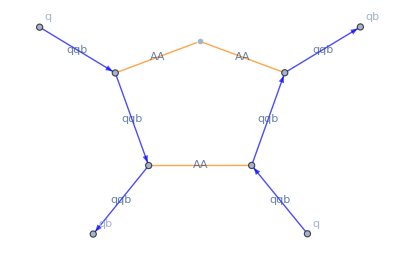
{4,-Graphics-}

```mathematica
PlotSuperindexDiagram[
DiagramsqbqqbqReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->False
]
PlotSuperindexDiagram[
DiagramsqbqqbqReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->True
]
```

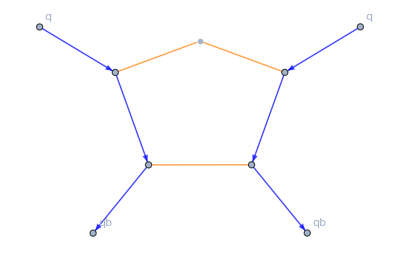
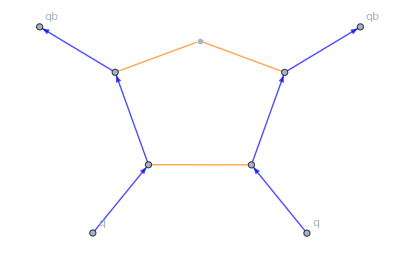
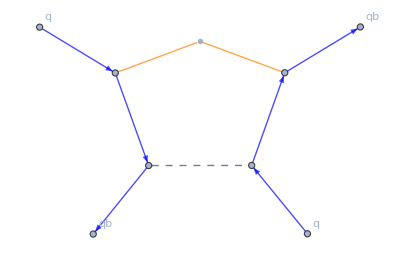
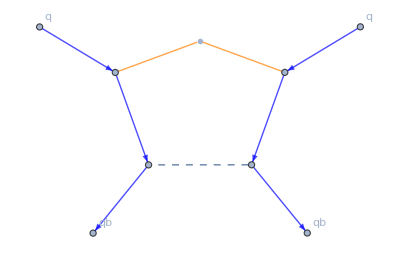
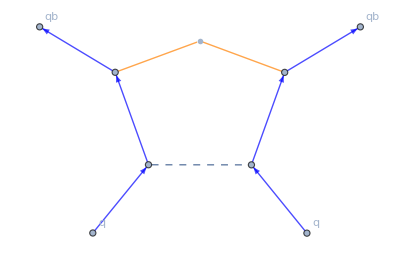
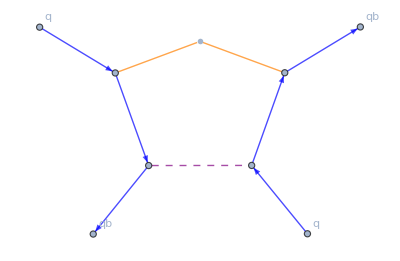
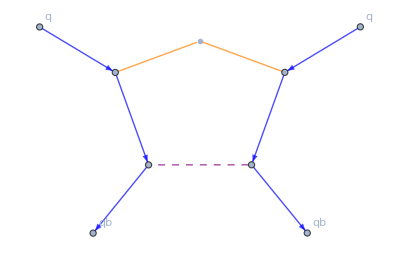
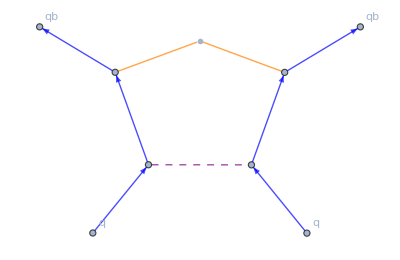
{{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-2,-Graphics-},{-2,-Graphics-},{-2,-Graphics-},{-2,-Graphics-}}

```mathematica
PlotSuperindexDiagram[
DiagramsqbqqbqReduced,SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple},c->Dotted},
"ShowEdgeLabels"->False
]
```

### Get Full diagrams and reroute the momenta for use in finite T setups

```mathematica
RerouteFermionicMomenta::usage
```

RerouteFermionicMomenta[diagrams, setup, derivativeList]

Reroute external fermionic momenta in diagrams such that Matsubara frequencies are automatically correctly routed.
If a closed fermion loop is present, the momentum in this loop is marked by attaching the character 'f' to it (i.e. q -> qf in such a loop).
The first argument to this function is a list of diagrams, the second one is the corresponding QMeS setup. The third argument is the derivative list that has been used to derive the set of diagrams.
Be aware, that the rerouting exploits momentum conservation - therefore, one of the external momenta may be eliminated if this is not yet the case.

```mathematica
DiagramsqbqqbqFull=SuperindexToFullDiagrams[DiagramsqbqqbqReduced,SetupfRGQCD,DerivativeListqbqqbq];
RerouteFermionicMomenta[DiagramsqbqqbqFull,SetupfRGQCD,DerivativeListqbqqbq]
```

{{4 GAA[{-q,v$37967,c$37967,q,v$37925,c$37925}] GAA[{q,v$37929,c$37929,-q,v$37922,c$37922}] GAA[{q,v$37951,c$37951,-q,v$37945,c$37945}] Gqqb[{-p-q,d$37936,c$37936,f$37936,p+q,d$37941,c$37941,f$37941}] Gqqb[{-p-q,d$37958,c$37958,f$37958,p+q,d$37963,c$37963,f$37963}] RdotAA[{-q,v$37922,c$37922,q,v$37925,c$37925}] ΓAqbq[{-q,v$37945,c$37945,p+q,d$37941,c$37941,f$37941,-p,d3,c3,f3}] ΓAqbq[{-q,v$37967,c$37967,p+q,d$37963,c$37963,f$37963,-p,d1,c1,f1}] ΓAqbq[{q,v$37929,c$37929,p,d4,c4,f4,-p-q,d$37936,c$37936,f$37936}] ΓAqbq[{q,v$37951,c$37951,p,d2,c2,f2,-p-q,d$37958,c$37958,f$37958}]},{2 GAA[{-q,v$38070,c$38070,q,v$38028,c$38028}] GAA[{q,v$38032,c$38032,-q,v$38025,c$38025}] GAA[{q,v$38054,c$38054,-q,v$38048,c$38048}] Gqqb[{-p-q,d$38061,c$38061,f$38061,p+q,d$38066,c$38066,f$38066}] Gqqb[{-p+q,d$38043,c$38043,f$38043,p-q,d$38038,c$38038,f$38038}] RdotAA[{-q,v$38025,c$38025,q,v$38028,c$38028}] ΓAqbq[{-q,v$38048,c$38048,p,d4,c4,f4,-p+q,d$38043,c$38043,f$38043}] ΓAqbq[{-q,v$38070,c$38070,p+q,d$38066,c$38066,f$38066,-p,d1,c1,f1}] ΓAqbq[{q,v$38032,c$38032,p-q,d$38038,c$38038,f$38038,-p,d3,c3,f3}] ΓAqbq[{q,v$38054,c$38054,p,d2,c2,f2,-p-q,d$38061,c$38061,f$38061}]},{-2 GAA[{-q,v$38146,c$38146,q,v$38153,c$38153}] GAA[{-q,v$38168,c$38168,q,v$38126,c$38126}] GAA[{q,v$38130,c$38130,-q,v$38123,c$38123}] Gqqb[{-p-q,d$38137,c$38137,f$38137,p+q,d$38142,c$38142,f$38142}] Gqqb[{-p+q,d$38163,c$38163,f$38163,p-q,d$38158,c$38158,f$38158}] RdotAA[{-q,v$38123,c$38123,q,v$38126,c$38126}] ΓAqbq[{-q,v$38146,c$38146,p+q,d$38142,c$38142,f$38142,-p,d3,c3,f3}] ΓAqbq[{-q,v$38168,c$38168,p,d4,c4,f4,-p+q,d$38163,c$38163,f$38163}] ΓAqbq[{q,v$38130,c$38130,p,d2,c2,f2,-p-q,d$38137,c$38137,f$38137}] ΓAqbq[{q,v$38153,c$38153,p-q,d$38158,c$38158,f$38158,-p,d1,c1,f1}]},{4 GAA[{-q,v$38266,c$38266,q,v$38224,c$38224}] GAA[{q,v$38228,c$38228,-q,v$38221,c$38221}] Gqqb[{-p-q,d$38235,c$38235,f$38235,p+q,d$38240,c$38240,f$38240}] Gqqb[{-p-q,d$38257,c$38257,f$38257,p+q,d$38262,c$38262,f$38262}] GΠΠ[{q,a$38250,-q,a$38244}] RdotAA[{-q,v$38221,c$38221,q,v$38224,c$38224}] ΓAqbq[{-q,v$38266,c$38266,p+q,d$38262,c$38262,f$38262,-p,d1,c1,f1}] ΓAqbq[{q,v$38228,c$38228,p,d4,c4,f4,-p-q,d$38235,c$38235,f$38235}] ΓΠqbq[{-q,a$38244,p+q,d$38240,c$38240,f$38240,-p,d3,c3,f3}] ΓΠqbq[{q,a$38250,p,d2,c2,f2,-p-q,d$38257,c$38257,f$38257}]},{2 GAA[{-q,v$38364,c$38364,q,v$38322,c$38322}] GAA[{q,v$38326,c$38326,-q,v$38319,c$38319}] Gqqb[{-p-q,d$38355,c$38355,f$38355,p+q,d$38360,c$38360,f$38360}] Gqqb[{-p+q,d$38337,c$38337,f$38337,p-q,d$38332,c$38332,f$38332}] GΠΠ[{q,a$38348,-q,a$38342}] RdotAA[{-q,v$38319,c$38319,q,v$38322,c$38322}] ΓAqbq[{-q,v$38364,c$38364,p+q,d$38360,c$38360,f$38360,-p,d1,c1,f1}] ΓAqbq[{q,v$38326,c$38326,p-q,d$38332,c$38332,f$38332,-p,d3,c3,f3}] ΓΠqbq[{-q,a$38342,p,d4,c4,f4,-p+q,d$38337,c$38337,f$38337}] ΓΠqbq[{q,a$38348,p,d2,c2,f2,-p-q,d$38355,c$38355,f$38355}]},{-2 GAA[{-q,v$38462,c$38462,q,v$38420,c$38420}] GAA[{q,v$38424,c$38424,-q,v$38417,c$38417}] Gqqb[{-p-q,d$38431,c$38431,f$38431,p+q,d$38436,c$38436,f$38436}] Gqqb[{-p+q,d$38457,c$38457,f$38457,p-q,d$38452,c$38452,f$38452}] GΠΠ[{-q,a$38440,q,a$38447}] RdotAA[{-q,v$38417,c$38417,q,v$38420,c$38420}] ΓAqbq[{-q,v$38462,c$38462,p,d4,c4,f4,-p+q,d$38457,c$38457,f$38457}] ΓAqbq[{q,v$38424,c$38424,p,d2,c2,f2,-p-q,d$38431,c$38431,f$38431}] ΓΠqbq[{-q,a$38440,p+q,d$38436,c$38436,f$38436,-p,d3,c3,f3}] ΓΠqbq[{q,a$38447,p-q,d$38452,c$38452,f$38452,-p,d1,c1,f1}]},{4 GAA[{-q,v$38558,c$38558,q,v$38518,c$38518}] GAA[{q,v$38522,c$38522,-q,v$38515,c$38515}] Gqqb[{-p-q,d$38529,c$38529,f$38529,p+q,d$38534,c$38534,f$38534}] Gqqb[{-p-q,d$38549,c$38549,f$38549,p+q,d$38554,c$38554,f$38554}] Gσσ[{q,-q}] RdotAA[{-q,v$38515,c$38515,q,v$38518,c$38518}] ΓAqbq[{-q,v$38558,c$38558,p+q,d$38554,c$38554,f$38554,-p,d1,c1,f1}] ΓAqbq[{q,v$38522,c$38522,p,d4,c4,f4,-p-q,d$38529,c$38529,f$38529}] Γσqbq[{-q,p+q,d$38534,c$38534,f$38534,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$38549,c$38549,f$38549}]},{2 GAA[{-q,v$38654,c$38654,q,v$38614,c$38614}] GAA[{q,v$38618,c$38618,-q,v$38611,c$38611}] Gqqb[{-p-q,d$38645,c$38645,f$38645,p+q,d$38650,c$38650,f$38650}] Gqqb[{-p+q,d$38629,c$38629,f$38629,p-q,d$38624,c$38624,f$38624}] Gσσ[{q,-q}] RdotAA[{-q,v$38611,c$38611,q,v$38614,c$38614}] ΓAqbq[{-q,v$38654,c$38654,p+q,d$38650,c$38650,f$38650,-p,d1,c1,f1}] ΓAqbq[{q,v$38618,c$38618,p-q,d$38624,c$38624,f$38624,-p,d3,c3,f3}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$38629,c$38629,f$38629}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$38645,c$38645,f$38645}]},{-2 GAA[{-q,v$38750,c$38750,q,v$38710,c$38710}] GAA[{q,v$38714,c$38714,-q,v$38707,c$38707}] Gqqb[{-p-q,d$38721,c$38721,f$38721,p+q,d$38726,c$38726,f$38726}] Gqqb[{-p+q,d$38745,c$38745,f$38745,p-q,d$38740,c$38740,f$38740}] Gσσ[{-q,q}] RdotAA[{-q,v$38707,c$38707,q,v$38710,c$38710}] ΓAqbq[{-q,v$38750,c$38750,p,d4,c4,f4,-p+q,d$38745,c$38745,f$38745}] ΓAqbq[{q,v$38714,c$38714,p,d2,c2,f2,-p-q,d$38721,c$38721,f$38721}] Γσqbq[{-q,p+q,d$38726,c$38726,f$38726,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$38740,c$38740,f$38740,-p,d1,c1,f1}]},{-4 GAA[{-q,v$38837,c$38837,q,v$38844,c$38844}] GAA[{q,v$38821,c$38821,-q,v$38815,c$38815}] Gqqb[{-p+q,d$38806,c$38806,f$38806,p-q,d$38849,c$38849,f$38849}] Gqqb[{-p+q,d$38810,c$38810,f$38810,p-q,d$38803,c$38803,f$38803}] Gqqb[{-p+q,d$38832,c$38832,f$38832,p-q,d$38827,c$38827,f$38827}] Rdotqbq[{p-q,d$38803,c$38803,f$38803,-p+q,d$38806,c$38806,f$38806}] ΓAqbq[{-q,v$38815,c$38815,p,d4,c4,f4,-p+q,d$38810,c$38810,f$38810}] ΓAqbq[{-q,v$38837,c$38837,p,d2,c2,f2,-p+q,d$38832,c$38832,f$38832}] ΓAqbq[{q,v$38821,c$38821,p-q,d$38827,c$38827,f$38827,-p,d3,c3,f3}] ΓAqbq[{q,v$38844,c$38844,p-q,d$38849,c$38849,f$38849,-p,d1,c1,f1}]},{-4 GAA[{-q,v$38935,c$38935,q,v$38942,c$38942}] GAA[{q,v$38919,c$38919,-q,v$38913,c$38913}] Gqqb[{-p-q,d$38926,c$38926,f$38926,p+q,d$38931,c$38931,f$38931}] Gqqb[{-p+q,d$38904,c$38904,f$38904,p-q,d$38947,c$38947,f$38947}] Gqqb[{-p+q,d$38908,c$38908,f$38908,p-q,d$38901,c$38901,f$38901}] Rdotqbq[{p-q,d$38901,c$38901,f$38901,-p+q,d$38904,c$38904,f$38904}] ΓAqbq[{-q,v$38913,c$38913,p,d4,c4,f4,-p+q,d$38908,c$38908,f$38908}] ΓAqbq[{-q,v$38935,c$38935,p+q,d$38931,c$38931,f$38931,-p,d3,c3,f3}] ΓAqbq[{q,v$38919,c$38919,p,d2,c2,f2,-p-q,d$38926,c$38926,f$38926}] ΓAqbq[{q,v$38942,c$38942,p-q,d$38947,c$38947,f$38947,-p,d1,c1,f1}]},{-4 GAA[{q,v$39017,c$39017,-q,v$39011,c$39011}] Gqqb[{-p+q,d$39002,c$39002,f$39002,p-q,d$39045,c$39045,f$39045}] Gqqb[{-p+q,d$39006,c$39006,f$39006,p-q,d$38999,c$38999,f$38999}] Gqqb[{-p+q,d$39028,c$39028,f$39028,p-q,d$39023,c$39023,f$39023}] GΠΠ[{-q,a$39033,q,a$39040}] Rdotqbq[{p-q,d$38999,c$38999,f$38999,-p+q,d$39002,c$39002,f$39002}] ΓAqbq[{-q,v$39011,c$39011,p,d4,c4,f4,-p+q,d$39006,c$39006,f$39006}] ΓAqbq[{q,v$39017,c$39017,p-q,d$39023,c$39023,f$39023,-p,d3,c3,f3}] ΓΠqbq[{-q,a$39033,p,d2,c2,f2,-p+q,d$39028,c$39028,f$39028}] ΓΠqbq[{q,a$39040,p-q,d$39045,c$39045,f$39045,-p,d1,c1,f1}]},{-4 GAA[{-q,v$39131,c$39131,q,v$39138,c$39138}] Gqqb[{-p+q,d$39100,c$39100,f$39100,p-q,d$39143,c$39143,f$39143}] Gqqb[{-p+q,d$39104,c$39104,f$39104,p-q,d$39097,c$39097,f$39097}] Gqqb[{-p+q,d$39126,c$39126,f$39126,p-q,d$39121,c$39121,f$39121}] GΠΠ[{q,a$39115,-q,a$39109}] Rdotqbq[{p-q,d$39097,c$39097,f$39097,-p+q,d$39100,c$39100,f$39100}] ΓAqbq[{-q,v$39131,c$39131,p,d2,c2,f2,-p+q,d$39126,c$39126,f$39126}] ΓAqbq[{q,v$39138,c$39138,p-q,d$39143,c$39143,f$39143,-p,d1,c1,f1}] ΓΠqbq[{-q,a$39109,p,d4,c4,f4,-p+q,d$39104,c$39104,f$39104}] ΓΠqbq[{q,a$39115,p-q,d$39121,c$39121,f$39121,-p,d3,c3,f3}]},{-4 GAA[{q,v$39213,c$39213,-q,v$39207,c$39207}] Gqqb[{-p-q,d$39220,c$39220,f$39220,p+q,d$39225,c$39225,f$39225}] Gqqb[{-p+q,d$39198,c$39198,f$39198,p-q,d$39241,c$39241,f$39241}] Gqqb[{-p+q,d$39202,c$39202,f$39202,p-q,d$39195,c$39195,f$39195}] GΠΠ[{-q,a$39229,q,a$39236}] Rdotqbq[{p-q,d$39195,c$39195,f$39195,-p+q,d$39198,c$39198,f$39198}] ΓAqbq[{-q,v$39207,c$39207,p,d4,c4,f4,-p+q,d$39202,c$39202,f$39202}] ΓAqbq[{q,v$39213,c$39213,p,d2,c2,f2,-p-q,d$39220,c$39220,f$39220}] ΓΠqbq[{-q,a$39229,p+q,d$39225,c$39225,f$39225,-p,d3,c3,f3}] ΓΠqbq[{q,a$39236,p-q,d$39241,c$39241,f$39241,-p,d1,c1,f1}]},{-4 GAA[{-q,v$39327,c$39327,q,v$39334,c$39334}] Gqqb[{-p-q,d$39318,c$39318,f$39318,p+q,d$39323,c$39323,f$39323}] Gqqb[{-p+q,d$39296,c$39296,f$39296,p-q,d$39339,c$39339,f$39339}] Gqqb[{-p+q,d$39300,c$39300,f$39300,p-q,d$39293,c$39293,f$39293}] GΠΠ[{q,a$39311,-q,a$39305}] Rdotqbq[{p-q,d$39293,c$39293,f$39293,-p+q,d$39296,c$39296,f$39296}] ΓAqbq[{-q,v$39327,c$39327,p+q,d$39323,c$39323,f$39323,-p,d3,c3,f3}] ΓAqbq[{q,v$39334,c$39334,p-q,d$39339,c$39339,f$39339,-p,d1,c1,f1}] ΓΠqbq[{-q,a$39305,p,d4,c4,f4,-p+q,d$39300,c$39300,f$39300}] ΓΠqbq[{q,a$39311,p,d2,c2,f2,-p-q,d$39318,c$39318,f$39318}]},{-4 GAA[{q,v$39409,c$39409,-q,v$39403,c$39403}] Gqqb[{-p+q,d$39394,c$39394,f$39394,p-q,d$39435,c$39435,f$39435}] Gqqb[{-p+q,d$39398,c$39398,f$39398,p-q,d$39391,c$39391,f$39391}] Gqqb[{-p+q,d$39420,c$39420,f$39420,p-q,d$39415,c$39415,f$39415}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$39391,c$39391,f$39391,-p+q,d$39394,c$39394,f$39394}] ΓAqbq[{-q,v$39403,c$39403,p,d4,c4,f4,-p+q,d$39398,c$39398,f$39398}] ΓAqbq[{q,v$39409,c$39409,p-q,d$39415,c$39415,f$39415,-p,d3,c3,f3}] Γσqbq[{-q,p,d2,c2,f2,-p+q,d$39420,c$39420,f$39420}] Γσqbq[{q,p-q,d$39435,c$39435,f$39435,-p,d1,c1,f1}]},{-4 GAA[{-q,v$39519,c$39519,q,v$39526,c$39526}] Gqqb[{-p+q,d$39490,c$39490,f$39490,p-q,d$39531,c$39531,f$39531}] Gqqb[{-p+q,d$39494,c$39494,f$39494,p-q,d$39487,c$39487,f$39487}] Gqqb[{-p+q,d$39514,c$39514,f$39514,p-q,d$39509,c$39509,f$39509}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$39487,c$39487,f$39487,-p+q,d$39490,c$39490,f$39490}] ΓAqbq[{-q,v$39519,c$39519,p,d2,c2,f2,-p+q,d$39514,c$39514,f$39514}] ΓAqbq[{q,v$39526,c$39526,p-q,d$39531,c$39531,f$39531,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$39494,c$39494,f$39494}] Γσqbq[{q,p-q,d$39509,c$39509,f$39509,-p,d3,c3,f3}]},{-4 GAA[{q,v$39601,c$39601,-q,v$39595,c$39595}] Gqqb[{-p-q,d$39608,c$39608,f$39608,p+q,d$39613,c$39613,f$39613}] Gqqb[{-p+q,d$39586,c$39586,f$39586,p-q,d$39627,c$39627,f$39627}] Gqqb[{-p+q,d$39590,c$39590,f$39590,p-q,d$39583,c$39583,f$39583}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$39583,c$39583,f$39583,-p+q,d$39586,c$39586,f$39586}] ΓAqbq[{-q,v$39595,c$39595,p,d4,c4,f4,-p+q,d$39590,c$39590,f$39590}] ΓAqbq[{q,v$39601,c$39601,p,d2,c2,f2,-p-q,d$39608,c$39608,f$39608}] Γσqbq[{-q,p+q,d$39613,c$39613,f$39613,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$39627,c$39627,f$39627,-p,d1,c1,f1}]},{-4 GAA[{-q,v$39711,c$39711,q,v$39718,c$39718}] Gqqb[{-p-q,d$39702,c$39702,f$39702,p+q,d$39707,c$39707,f$39707}] Gqqb[{-p+q,d$39682,c$39682,f$39682,p-q,d$39723,c$39723,f$39723}] Gqqb[{-p+q,d$39686,c$39686,f$39686,p-q,d$39679,c$39679,f$39679}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$39679,c$39679,f$39679,-p+q,d$39682,c$39682,f$39682}] ΓAqbq[{-q,v$39711,c$39711,p+q,d$39707,c$39707,f$39707,-p,d3,c3,f3}] ΓAqbq[{q,v$39718,c$39718,p-q,d$39723,c$39723,f$39723,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$39686,c$39686,f$39686}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$39702,c$39702,f$39702}]},{-4 Gqqb[{-p+q,d$39778,c$39778,f$39778,p-q,d$39821,c$39821,f$39821}] Gqqb[{-p+q,d$39782,c$39782,f$39782,p-q,d$39775,c$39775,f$39775}] Gqqb[{-p+q,d$39804,c$39804,f$39804,p-q,d$39799,c$39799,f$39799}] GΠΠ[{-q,a$39809,q,a$39816}] GΠΠ[{q,a$39793,-q,a$39787}] Rdotqbq[{p-q,d$39775,c$39775,f$39775,-p+q,d$39778,c$39778,f$39778}] ΓΠqbq[{-q,a$39787,p,d4,c4,f4,-p+q,d$39782,c$39782,f$39782}] ΓΠqbq[{-q,a$39809,p,d2,c2,f2,-p+q,d$39804,c$39804,f$39804}] ΓΠqbq[{q,a$39793,p-q,d$39799,c$39799,f$39799,-p,d3,c3,f3}] ΓΠqbq[{q,a$39816,p-q,d$39821,c$39821,f$39821,-p,d1,c1,f1}]},{-4 Gqqb[{-p-q,d$39898,c$39898,f$39898,p+q,d$39903,c$39903,f$39903}] Gqqb[{-p+q,d$39876,c$39876,f$39876,p-q,d$39919,c$39919,f$39919}] Gqqb[{-p+q,d$39880,c$39880,f$39880,p-q,d$39873,c$39873,f$39873}] GΠΠ[{-q,a$39907,q,a$39914}] GΠΠ[{q,a$39891,-q,a$39885}] Rdotqbq[{p-q,d$39873,c$39873,f$39873,-p+q,d$39876,c$39876,f$39876}] ΓΠqbq[{-q,a$39885,p,d4,c4,f4,-p+q,d$39880,c$39880,f$39880}] ΓΠqbq[{-q,a$39907,p+q,d$39903,c$39903,f$39903,-p,d3,c3,f3}] ΓΠqbq[{q,a$39891,p,d2,c2,f2,-p-q,d$39898,c$39898,f$39898}] ΓΠqbq[{q,a$39914,p-q,d$39919,c$39919,f$39919,-p,d1,c1,f1}]},{-4 Gqqb[{-p+q,d$39974,c$39974,f$39974,p-q,d$40015,c$40015,f$40015}] Gqqb[{-p+q,d$39978,c$39978,f$39978,p-q,d$39971,c$39971,f$39971}] Gqqb[{-p+q,d$40000,c$40000,f$40000,p-q,d$39995,c$39995,f$39995}] GΠΠ[{q,a$39989,-q,a$39983}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$39971,c$39971,f$39971,-p+q,d$39974,c$39974,f$39974}] ΓΠqbq[{-q,a$39983,p,d4,c4,f4,-p+q,d$39978,c$39978,f$39978}] ΓΠqbq[{q,a$39989,p-q,d$39995,c$39995,f$39995,-p,d3,c3,f3}] Γσqbq[{-q,p,d2,c2,f2,-p+q,d$40000,c$40000,f$40000}] Γσqbq[{q,p-q,d$40015,c$40015,f$40015,-p,d1,c1,f1}]},{-4 Gqqb[{-p+q,d$40070,c$40070,f$40070,p-q,d$40111,c$40111,f$40111}] Gqqb[{-p+q,d$40074,c$40074,f$40074,p-q,d$40067,c$40067,f$40067}] Gqqb[{-p+q,d$40094,c$40094,f$40094,p-q,d$40089,c$40089,f$40089}] GΠΠ[{-q,a$40099,q,a$40106}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$40067,c$40067,f$40067,-p+q,d$40070,c$40070,f$40070}] ΓΠqbq[{-q,a$40099,p,d2,c2,f2,-p+q,d$40094,c$40094,f$40094}] ΓΠqbq[{q,a$40106,p-q,d$40111,c$40111,f$40111,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$40074,c$40074,f$40074}] Γσqbq[{q,p-q,d$40089,c$40089,f$40089,-p,d3,c3,f3}]},{-4 Gqqb[{-p-q,d$40188,c$40188,f$40188,p+q,d$40193,c$40193,f$40193}] Gqqb[{-p+q,d$40166,c$40166,f$40166,p-q,d$40207,c$40207,f$40207}] Gqqb[{-p+q,d$40170,c$40170,f$40170,p-q,d$40163,c$40163,f$40163}] GΠΠ[{q,a$40181,-q,a$40175}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$40163,c$40163,f$40163,-p+q,d$40166,c$40166,f$40166}] ΓΠqbq[{-q,a$40175,p,d4,c4,f4,-p+q,d$40170,c$40170,f$40170}] ΓΠqbq[{q,a$40181,p,d2,c2,f2,-p-q,d$40188,c$40188,f$40188}] Γσqbq[{-q,p+q,d$40193,c$40193,f$40193,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$40207,c$40207,f$40207,-p,d1,c1,f1}]},{-4 Gqqb[{-p-q,d$40282,c$40282,f$40282,p+q,d$40287,c$40287,f$40287}] Gqqb[{-p+q,d$40262,c$40262,f$40262,p-q,d$40303,c$40303,f$40303}] Gqqb[{-p+q,d$40266,c$40266,f$40266,p-q,d$40259,c$40259,f$40259}] GΠΠ[{-q,a$40291,q,a$40298}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$40259,c$40259,f$40259,-p+q,d$40262,c$40262,f$40262}] ΓΠqbq[{-q,a$40291,p+q,d$40287,c$40287,f$40287,-p,d3,c3,f3}] ΓΠqbq[{q,a$40298,p-q,d$40303,c$40303,f$40303,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$40266,c$40266,f$40266}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$40282,c$40282,f$40282}]},{-4 Gqqb[{-p+q,d$40358,c$40358,f$40358,p-q,d$40397,c$40397,f$40397}] Gqqb[{-p+q,d$40362,c$40362,f$40362,p-q,d$40355,c$40355,f$40355}] Gqqb[{-p+q,d$40382,c$40382,f$40382,p-q,d$40377,c$40377,f$40377}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$40355,c$40355,f$40355,-p+q,d$40358,c$40358,f$40358}] Γσqbq[{-q,p,d2,c2,f2,-p+q,d$40382,c$40382,f$40382}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$40362,c$40362,f$40362}] Γσqbq[{q,p-q,d$40377,c$40377,f$40377,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$40397,c$40397,f$40397,-p,d1,c1,f1}]},{-4 Gqqb[{-p-q,d$40472,c$40472,f$40472,p+q,d$40477,c$40477,f$40477}] Gqqb[{-p+q,d$40452,c$40452,f$40452,p-q,d$40491,c$40491,f$40491}] Gqqb[{-p+q,d$40456,c$40456,f$40456,p-q,d$40449,c$40449,f$40449}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$40449,c$40449,f$40449,-p+q,d$40452,c$40452,f$40452}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$40456,c$40456,f$40456}] Γσqbq[{-q,p+q,d$40477,c$40477,f$40477,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$40472,c$40472,f$40472}] Γσqbq[{q,p-q,d$40491,c$40491,f$40491,-p,d1,c1,f1}]},{4 GAA[{q,v$40572,c$40572,-q,v$40566,c$40566}] Gqqb[{-p-q,d$40557,c$40557,f$40557,p+q,d$40562,c$40562,f$40562}] Gqqb[{-p-q,d$40579,c$40579,f$40579,p+q,d$40584,c$40584,f$40584}] GΠΠ[{-q,a$40588,q,a$40546}] GΠΠ[{q,a$40550,-q,a$40543}] RdotΠΠ[{-q,a$40543,q,a$40546}] ΓAqbq[{-q,v$40566,c$40566,p+q,d$40562,c$40562,f$40562,-p,d3,c3,f3}] ΓAqbq[{q,v$40572,c$40572,p,d2,c2,f2,-p-q,d$40579,c$40579,f$40579}] ΓΠqbq[{-q,a$40588,p+q,d$40584,c$40584,f$40584,-p,d1,c1,f1}] ΓΠqbq[{q,a$40550,p,d4,c4,f4,-p-q,d$40557,c$40557,f$40557}]},{2 GAA[{q,v$40670,c$40670,-q,v$40664,c$40664}] Gqqb[{-p-q,d$40677,c$40677,f$40677,p+q,d$40682,c$40682,f$40682}] Gqqb[{-p+q,d$40659,c$40659,f$40659,p-q,d$40654,c$40654,f$40654}] GΠΠ[{-q,a$40686,q,a$40644}] GΠΠ[{q,a$40648,-q,a$40641}] RdotΠΠ[{-q,a$40641,q,a$40644}] ΓAqbq[{-q,v$40664,c$40664,p,d4,c4,f4,-p+q,d$40659,c$40659,f$40659}] ΓAqbq[{q,v$40670,c$40670,p,d2,c2,f2,-p-q,d$40677,c$40677,f$40677}] ΓΠqbq[{-q,a$40686,p+q,d$40682,c$40682,f$40682,-p,d1,c1,f1}] ΓΠqbq[{q,a$40648,p-q,d$40654,c$40654,f$40654,-p,d3,c3,f3}]},{-2 GAA[{-q,v$40762,c$40762,q,v$40769,c$40769}] Gqqb[{-p-q,d$40753,c$40753,f$40753,p+q,d$40758,c$40758,f$40758}] Gqqb[{-p+q,d$40779,c$40779,f$40779,p-q,d$40774,c$40774,f$40774}] GΠΠ[{-q,a$40784,q,a$40742}] GΠΠ[{q,a$40746,-q,a$40739}] RdotΠΠ[{-q,a$40739,q,a$40742}] ΓAqbq[{-q,v$40762,c$40762,p+q,d$40758,c$40758,f$40758,-p,d3,c3,f3}] ΓAqbq[{q,v$40769,c$40769,p-q,d$40774,c$40774,f$40774,-p,d1,c1,f1}] ΓΠqbq[{-q,a$40784,p,d4,c4,f4,-p+q,d$40779,c$40779,f$40779}] ΓΠqbq[{q,a$40746,p,d2,c2,f2,-p-q,d$40753,c$40753,f$40753}]},{4 Gqqb[{-p-q,d$40851,c$40851,f$40851,p+q,d$40856,c$40856,f$40856}] Gqqb[{-p-q,d$40873,c$40873,f$40873,p+q,d$40878,c$40878,f$40878}] GΠΠ[{-q,a$40882,q,a$40840}] GΠΠ[{q,a$40844,-q,a$40837}] GΠΠ[{q,a$40866,-q,a$40860}] RdotΠΠ[{-q,a$40837,q,a$40840}] ΓΠqbq[{-q,a$40860,p+q,d$40856,c$40856,f$40856,-p,d3,c3,f3}] ΓΠqbq[{-q,a$40882,p+q,d$40878,c$40878,f$40878,-p,d1,c1,f1}] ΓΠqbq[{q,a$40844,p,d4,c4,f4,-p-q,d$40851,c$40851,f$40851}] ΓΠqbq[{q,a$40866,p,d2,c2,f2,-p-q,d$40873,c$40873,f$40873}]},{2 Gqqb[{-p-q,d$40971,c$40971,f$40971,p+q,d$40976,c$40976,f$40976}] Gqqb[{-p+q,d$40953,c$40953,f$40953,p-q,d$40948,c$40948,f$40948}] GΠΠ[{-q,a$40980,q,a$40938}] GΠΠ[{q,a$40942,-q,a$40935}] GΠΠ[{q,a$40964,-q,a$40958}] RdotΠΠ[{-q,a$40935,q,a$40938}] ΓΠqbq[{-q,a$40958,p,d4,c4,f4,-p+q,d$40953,c$40953,f$40953}] ΓΠqbq[{-q,a$40980,p+q,d$40976,c$40976,f$40976,-p,d1,c1,f1}] ΓΠqbq[{q,a$40942,p-q,d$40948,c$40948,f$40948,-p,d3,c3,f3}] ΓΠqbq[{q,a$40964,p,d2,c2,f2,-p-q,d$40971,c$40971,f$40971}]},{-2 Gqqb[{-p-q,d$41047,c$41047,f$41047,p+q,d$41052,c$41052,f$41052}] Gqqb[{-p+q,d$41073,c$41073,f$41073,p-q,d$41068,c$41068,f$41068}] GΠΠ[{-q,a$41056,q,a$41063}] GΠΠ[{-q,a$41078,q,a$41036}] GΠΠ[{q,a$41040,-q,a$41033}] RdotΠΠ[{-q,a$41033,q,a$41036}] ΓΠqbq[{-q,a$41056,p+q,d$41052,c$41052,f$41052,-p,d3,c3,f3}] ΓΠqbq[{-q,a$41078,p,d4,c4,f4,-p+q,d$41073,c$41073,f$41073}] ΓΠqbq[{q,a$41040,p,d2,c2,f2,-p-q,d$41047,c$41047,f$41047}] ΓΠqbq[{q,a$41063,p-q,d$41068,c$41068,f$41068,-p,d1,c1,f1}]},{4 Gqqb[{-p-q,d$41145,c$41145,f$41145,p+q,d$41150,c$41150,f$41150}] Gqqb[{-p-q,d$41165,c$41165,f$41165,p+q,d$41170,c$41170,f$41170}] GΠΠ[{-q,a$41174,q,a$41134}] GΠΠ[{q,a$41138,-q,a$41131}] Gσσ[{q,-q}] RdotΠΠ[{-q,a$41131,q,a$41134}] ΓΠqbq[{-q,a$41174,p+q,d$41170,c$41170,f$41170,-p,d1,c1,f1}] ΓΠqbq[{q,a$41138,p,d4,c4,f4,-p-q,d$41145,c$41145,f$41145}] Γσqbq[{-q,p+q,d$41150,c$41150,f$41150,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$41165,c$41165,f$41165}]},{2 Gqqb[{-p-q,d$41261,c$41261,f$41261,p+q,d$41266,c$41266,f$41266}] Gqqb[{-p+q,d$41245,c$41245,f$41245,p-q,d$41240,c$41240,f$41240}] GΠΠ[{-q,a$41270,q,a$41230}] GΠΠ[{q,a$41234,-q,a$41227}] Gσσ[{q,-q}] RdotΠΠ[{-q,a$41227,q,a$41230}] ΓΠqbq[{-q,a$41270,p+q,d$41266,c$41266,f$41266,-p,d1,c1,f1}] ΓΠqbq[{q,a$41234,p-q,d$41240,c$41240,f$41240,-p,d3,c3,f3}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$41245,c$41245,f$41245}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$41261,c$41261,f$41261}]},{-2 Gqqb[{-p-q,d$41337,c$41337,f$41337,p+q,d$41342,c$41342,f$41342}] Gqqb[{-p+q,d$41361,c$41361,f$41361,p-q,d$41356,c$41356,f$41356}] GΠΠ[{-q,a$41366,q,a$41326}] GΠΠ[{q,a$41330,-q,a$41323}] Gσσ[{-q,q}] RdotΠΠ[{-q,a$41323,q,a$41326}] ΓΠqbq[{-q,a$41366,p,d4,c4,f4,-p+q,d$41361,c$41361,f$41361}] ΓΠqbq[{q,a$41330,p,d2,c2,f2,-p-q,d$41337,c$41337,f$41337}] Γσqbq[{-q,p+q,d$41342,c$41342,f$41342,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$41356,c$41356,f$41356,-p,d1,c1,f1}]},{4 GAA[{q,v$41445,c$41445,-q,v$41439,c$41439}] Gqqb[{-p-q,d$41430,c$41430,f$41430,p+q,d$41435,c$41435,f$41435}] Gqqb[{-p-q,d$41452,c$41452,f$41452,p+q,d$41457,c$41457,f$41457}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓAqbq[{-q,v$41439,c$41439,p+q,d$41435,c$41435,f$41435,-p,d3,c3,f3}] ΓAqbq[{q,v$41445,c$41445,p,d2,c2,f2,-p-q,d$41452,c$41452,f$41452}] Γσqbq[{-q,p+q,d$41457,c$41457,f$41457,-p,d1,c1,f1}] Γσqbq[{q,p,d4,c4,f4,-p-q,d$41430,c$41430,f$41430}]},{2 GAA[{q,v$41539,c$41539,-q,v$41533,c$41533}] Gqqb[{-p-q,d$41546,c$41546,f$41546,p+q,d$41551,c$41551,f$41551}] Gqqb[{-p+q,d$41528,c$41528,f$41528,p-q,d$41523,c$41523,f$41523}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓAqbq[{-q,v$41533,c$41533,p,d4,c4,f4,-p+q,d$41528,c$41528,f$41528}] ΓAqbq[{q,v$41539,c$41539,p,d2,c2,f2,-p-q,d$41546,c$41546,f$41546}] Γσqbq[{-q,p+q,d$41551,c$41551,f$41551,-p,d1,c1,f1}] Γσqbq[{q,p-q,d$41523,c$41523,f$41523,-p,d3,c3,f3}]},{-2 GAA[{-q,v$41627,c$41627,q,v$41634,c$41634}] Gqqb[{-p-q,d$41618,c$41618,f$41618,p+q,d$41623,c$41623,f$41623}] Gqqb[{-p+q,d$41644,c$41644,f$41644,p-q,d$41639,c$41639,f$41639}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓAqbq[{-q,v$41627,c$41627,p+q,d$41623,c$41623,f$41623,-p,d3,c3,f3}] ΓAqbq[{q,v$41634,c$41634,p-q,d$41639,c$41639,f$41639,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$41644,c$41644,f$41644}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$41618,c$41618,f$41618}]},{4 Gqqb[{-p-q,d$41712,c$41712,f$41712,p+q,d$41717,c$41717,f$41717}] Gqqb[{-p-q,d$41734,c$41734,f$41734,p+q,d$41739,c$41739,f$41739}] GΠΠ[{q,a$41727,-q,a$41721}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{-q,a$41721,p+q,d$41717,c$41717,f$41717,-p,d3,c3,f3}] ΓΠqbq[{q,a$41727,p,d2,c2,f2,-p-q,d$41734,c$41734,f$41734}] Γσqbq[{-q,p+q,d$41739,c$41739,f$41739,-p,d1,c1,f1}] Γσqbq[{q,p,d4,c4,f4,-p-q,d$41712,c$41712,f$41712}]},{2 Gqqb[{-p-q,d$41828,c$41828,f$41828,p+q,d$41833,c$41833,f$41833}] Gqqb[{-p+q,d$41810,c$41810,f$41810,p-q,d$41805,c$41805,f$41805}] GΠΠ[{q,a$41821,-q,a$41815}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{-q,a$41815,p,d4,c4,f4,-p+q,d$41810,c$41810,f$41810}] ΓΠqbq[{q,a$41821,p,d2,c2,f2,-p-q,d$41828,c$41828,f$41828}] Γσqbq[{-q,p+q,d$41833,c$41833,f$41833,-p,d1,c1,f1}] Γσqbq[{q,p-q,d$41805,c$41805,f$41805,-p,d3,c3,f3}]},{-2 Gqqb[{-p-q,d$41900,c$41900,f$41900,p+q,d$41905,c$41905,f$41905}] Gqqb[{-p+q,d$41926,c$41926,f$41926,p-q,d$41921,c$41921,f$41921}] GΠΠ[{-q,a$41909,q,a$41916}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{-q,a$41909,p+q,d$41905,c$41905,f$41905,-p,d3,c3,f3}] ΓΠqbq[{q,a$41916,p-q,d$41921,c$41921,f$41921,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$41926,c$41926,f$41926}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$41900,c$41900,f$41900}]},{4 Gqqb[{-p-q,d$41994,c$41994,f$41994,p+q,d$41999,c$41999,f$41999}] Gqqb[{-p-q,d$42014,c$42014,f$42014,p+q,d$42019,c$42019,f$42019}] Gσσ[{-q,q}] Gσσ[{q,-q}]^2 Rdotσσ[{-q,q}] Γσqbq[{-q,p+q,d$41999,c$41999,f$41999,-p,d3,c3,f3}] Γσqbq[{-q,p+q,d$42019,c$42019,f$42019,-p,d1,c1,f1}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$42014,c$42014,f$42014}] Γσqbq[{q,p,d4,c4,f4,-p-q,d$41994,c$41994,f$41994}]},{2 Gqqb[{-p-q,d$42106,c$42106,f$42106,p+q,d$42111,c$42111,f$42111}] Gqqb[{-p+q,d$42090,c$42090,f$42090,p-q,d$42085,c$42085,f$42085}] Gσσ[{-q,q}] Gσσ[{q,-q}]^2 Rdotσσ[{-q,q}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$42090,c$42090,f$42090}] Γσqbq[{-q,p+q,d$42111,c$42111,f$42111,-p,d1,c1,f1}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$42106,c$42106,f$42106}] Γσqbq[{q,p-q,d$42085,c$42085,f$42085,-p,d3,c3,f3}]},{-2 Gqqb[{-p-q,d$42178,c$42178,f$42178,p+q,d$42183,c$42183,f$42183}] Gqqb[{-p+q,d$42202,c$42202,f$42202,p-q,d$42197,c$42197,f$42197}] Gσσ[{-q,q}]^2 Gσσ[{q,-q}] Rdotσσ[{-q,q}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$42202,c$42202,f$42202}] Γσqbq[{-q,p+q,d$42183,c$42183,f$42183,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$42178,c$42178,f$42178}] Γσqbq[{q,p-q,d$42197,c$42197,f$42197,-p,d1,c1,f1}]},{4 Gqqb[{-p-q,d$42285,c$42285,f$42285,p+q,d$42290,c$42290,f$42290}] GΠΠ[{-q,a$42294,q,a$42262}] GΠΠ[{q,a$42266,-q,a$42259}] GΠΠ[{q,a$42278,-q,a$42272}] RdotΠΠ[{-q,a$42259,q,a$42262}] ΓΠqbq[{-q,a$42294,p+q,d$42290,c$42290,f$42290,-p,d1,c1,f1}] ΓΠqbq[{q,a$42278,p,d2,c2,f2,-p-q,d$42285,c$42285,f$42285}] ΓΠΠqbq[{q,a$42266,-q,a$42272,p,d4,c4,f4,-p,d3,c3,f3}]},{-4 Gqqb[{-p+q,d$42369,c$42369,f$42369,p-q,d$42364,c$42364,f$42364}] GΠΠ[{-q,a$42352,q,a$42359}] GΠΠ[{-q,a$42374,q,a$42342}] GΠΠ[{q,a$42346,-q,a$42339}] RdotΠΠ[{-q,a$42339,q,a$42342}] ΓΠqbq[{-q,a$42374,p,d4,c4,f4,-p+q,d$42369,c$42369,f$42369}] ΓΠqbq[{q,a$42359,p-q,d$42364,c$42364,f$42364,-p,d1,c1,f1}] ΓΠΠqbq[{q,a$42346,-q,a$42352,p,d2,c2,f2,-p,d3,c3,f3}]},{4 Gqqb[{-p-q,d$42443,c$42443,f$42443,p+q,d$42448,c$42448,f$42448}] GΠΠ[{-q,a$42452,q,a$42422}] GΠΠ[{q,a$42426,-q,a$42419}] Gσσ[{q,-q}] RdotΠΠ[{-q,a$42419,q,a$42422}] ΓΠqbq[{-q,a$42452,p+q,d$42448,c$42448,f$42448,-p,d1,c1,f1}] ΓΠσqbq[{q,a$42426,-q,p,d4,c4,f4,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$42443,c$42443,f$42443}]},{-4 Gqqb[{-p+q,d$42525,c$42525,f$42525,p-q,d$42520,c$42520,f$42520}] GΠΠ[{-q,a$42530,q,a$42500}] GΠΠ[{q,a$42504,-q,a$42497}] Gσσ[{-q,q}] RdotΠΠ[{-q,a$42497,q,a$42500}] ΓΠqbq[{-q,a$42530,p,d4,c4,f4,-p+q,d$42525,c$42525,f$42525}] ΓΠσqbq[{q,a$42504,-q,p,d2,c2,f2,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$42520,c$42520,f$42520,-p,d1,c1,f1}]},{4 Gqqb[{-p-q,d$42598,c$42598,f$42598,p+q,d$42603,c$42603,f$42603}] GΠΠ[{q,a$42591,-q,a$42584}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{q,a$42591,p,d2,c2,f2,-p-q,d$42598,c$42598,f$42598}] ΓΠσqbq[{-q,a$42584,q,p,d4,c4,f4,-p,d3,c3,f3}] Γσqbq[{-q,p+q,d$42603,c$42603,f$42603,-p,d1,c1,f1}]},{-4 Gqqb[{-p+q,d$42678,c$42678,f$42678,p-q,d$42673,c$42673,f$42673}] GΠΠ[{-q,a$42660,q,a$42668}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{q,a$42668,p-q,d$42673,c$42673,f$42673,-p,d1,c1,f1}] ΓΠσqbq[{-q,a$42660,q,p,d2,c2,f2,-p,d3,c3,f3}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$42678,c$42678,f$42678}]},{4 Gqqb[{-p-q,d$42748,c$42748,f$42748,p+q,d$42753,c$42753,f$42753}] Gσσ[{-q,q}] Gσσ[{q,-q}]^2 Rdotσσ[{-q,q}] Γσqbq[{-q,p+q,d$42753,c$42753,f$42753,-p,d1,c1,f1}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$42748,c$42748,f$42748}] Γσσqbq[{q,-q,p,d4,c4,f4,-p,d3,c3,f3}]},{-4 Gqqb[{-p+q,d$42826,c$42826,f$42826,p-q,d$42821,c$42821,f$42821}] Gσσ[{-q,q}]^2 Gσσ[{q,-q}] Rdotσσ[{-q,q}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$42826,c$42826,f$42826}] Γσqbq[{q,p-q,d$42821,c$42821,f$42821,-p,d1,c1,f1}] Γσσqbq[{q,-q,p,d2,c2,f2,-p,d3,c3,f3}]},{-4 Gqqb[{-p+q,d$42878,c$42878,f$42878,p-q,d$42911,c$42911,f$42911}] Gqqb[{-p+q,d$42882,c$42882,f$42882,p-q,d$42875,c$42875,f$42875}] GΠΠ[{-q,a$42899,q,a$42906}] GΠΠ[{q,a$42893,-q,a$42887}] Rdotqbq[{p-q,d$42875,c$42875,f$42875,-p+q,d$42878,c$42878,f$42878}] ΓΠqbq[{-q,a$42887,p,d4,c4,f4,-p+q,d$42882,c$42882,f$42882}] ΓΠqbq[{q,a$42906,p-q,d$42911,c$42911,f$42911,-p,d1,c1,f1}] ΓΠΠqbq[{q,a$42893,-q,a$42899,p,d2,c2,f2,-p,d3,c3,f3}]},{-4 Gqqb[{-p+q,d$42958,c$42958,f$42958,p-q,d$42989,c$42989,f$42989}] Gqqb[{-p+q,d$42962,c$42962,f$42962,p-q,d$42955,c$42955,f$42955}] GΠΠ[{q,a$42973,-q,a$42967}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$42955,c$42955,f$42955,-p+q,d$42958,c$42958,f$42958}] ΓΠqbq[{-q,a$42967,p,d4,c4,f4,-p+q,d$42962,c$42962,f$42962}] ΓΠσqbq[{q,a$42973,-q,p,d2,c2,f2,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$42989,c$42989,f$42989,-p,d1,c1,f1}]},{-4 Gqqb[{-p+q,d$43036,c$43036,f$43036,p-q,d$43067,c$43067,f$43067}] Gqqb[{-p+q,d$43040,c$43040,f$43040,p-q,d$43033,c$43033,f$43033}] GΠΠ[{-q,a$43054,q,a$43062}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$43033,c$43033,f$43033,-p+q,d$43036,c$43036,f$43036}] ΓΠqbq[{q,a$43062,p-q,d$43067,c$43067,f$43067,-p,d1,c1,f1}] ΓΠσqbq[{-q,a$43054,q,p,d2,c2,f2,-p,d3,c3,f3}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$43040,c$43040,f$43040}]},{-4 Gqqb[{-p+q,d$43114,c$43114,f$43114,p-q,d$43143,c$43143,f$43143}] Gqqb[{-p+q,d$43118,c$43118,f$43118,p-q,d$43111,c$43111,f$43111}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$43111,c$43111,f$43111,-p+q,d$43114,c$43114,f$43114}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$43118,c$43118,f$43118}] Γσqbq[{q,p-q,d$43143,c$43143,f$43143,-p,d1,c1,f1}] Γσσqbq[{q,-q,p,d2,c2,f2,-p,d3,c3,f3}]},{-2 GΠΠ[{-q,a$43200,q,a$43207}] GΠΠ[{-q,a$43212,q,a$43190}] GΠΠ[{q,a$43194,-q,a$43187}] RdotΠΠ[{-q,a$43187,q,a$43190}] ΓΠΠqbq[{q,a$43194,-q,a$43200,p,d2,c2,f2,-p,d3,c3,f3}] ΓΠΠqbq[{q,a$43207,-q,a$43212,p,d4,c4,f4,-p,d1,c1,f1}]},{-2 GΠΠ[{-q,a$43271,q,a$43252}] GΠΠ[{q,a$43256,-q,a$43249}] Gσσ[{-q,q}] RdotΠΠ[{-q,a$43249,q,a$43252}] ΓΠσqbq[{-q,a$43271,q,p,d4,c4,f4,-p,d1,c1,f1}] ΓΠσqbq[{q,a$43256,-q,p,d2,c2,f2,-p,d3,c3,f3}]},{-2 GΠΠ[{-q,a$43318,q,a$43326}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠσqbq[{-q,a$43318,q,p,d2,c2,f2,-p,d3,c3,f3}] ΓΠσqbq[{q,a$43326,-q,p,d4,c4,f4,-p,d1,c1,f1}]},{-2 Gσσ[{-q,q}]^2 Gσσ[{q,-q}] Rdotσσ[{-q,q}] Γσσqbq[{q,-q,p,d2,c2,f2,-p,d3,c3,f3}] Γσσqbq[{q,-q,p,d4,c4,f4,-p,d1,c1,f1}]}}

## FRG Equations: Three-gluon vertex

### Derive flow equation of three-gluon vertex

```mathematica
DerivativeListAAA= {A[p1,{v1,c1}],A[p2,{v3,c3}],A[p3,{v3,c3}]};
DiagramsAAA=DeriveFunctionalEquation[SetupfRGQCD,DerivativeListAAA,"OutputLevel"->"SuperindexDiagrams"];
DiagramsAAA//Length
```

48

### Reduce the number of diagrams on the symmetric point

```mathematica
ReduceIdenticalFlowDiagrams::usage
```

ReduceIdenticalFlowDiagrams[diagrams,derivativeList,symmetries]

Reduce a set of flow equations by matching identical topologies and/or by utilizing a given set of symmetries.
The user has to supply the list of derivatives (i.e. external legs in the diagrams). Then, the symmetries are specified in the following way:
symmetries = {
	{ {1, 3}, Minus},
	{ {2, 4}, Minus}
	{ {1, 3}, {2, 4}, Plus},
}
Here, two antisymmetries (as specified by the Minus) are given, which consist of a single cycle each (1,3) and (2,4). These integers refer to the legs as given in derivativeList (in order).
ReduceIdenticalFlowDiagrams does not construct all symmetries from the given ones - therefore, the full symmetry group needs to be specified. Therefore, we also supply the symmetry consisting of both cycles explicitly in the third line.

```mathematica
symmetries={
{{1,2},Plus},
{{2,3},Plus},
{{3,1},Plus},
{{1,2,3},Plus},
{{3,2,1},Plus}
};
DiagramsAAAReduced=ReduceIdenticalFlowDiagrams[DiagramsAAA,DerivativeListAAA,symmetries];
DiagramsAAAReduced//Length
```

5

### Plot the resulting diagrams

```mathematica
PlotSuperindexDiagram::usage
```

PlotSuperindexDiagram[diagram, setup, options]

Plot one or multiple superindex diagrams. The first argument to this function are the diagram(s), the second one is the corresponding QMeS setup.
The diagram(s) have to be superindex diagram(s).

The options for the function PlotSuperindexDiagram are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.

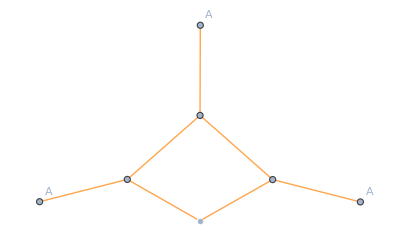
{-3,-Graphics-}

```mathematica
PlotSuperindexDiagram[
DiagramsAAAReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->False
]
```

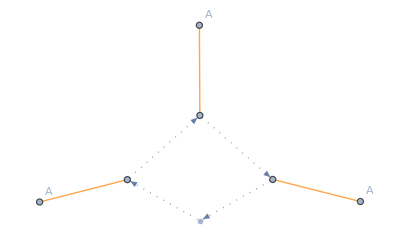
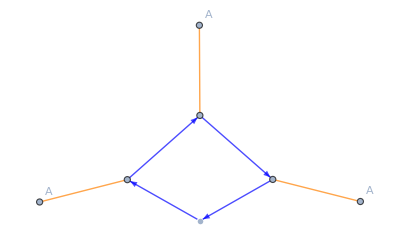
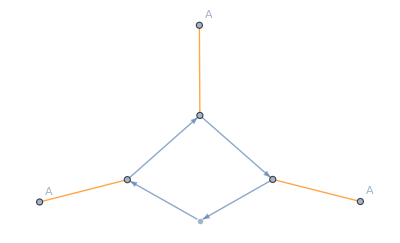
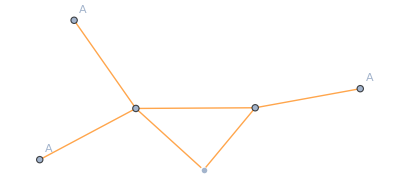
{{-3,-Graphics-},{-6,-Graphics-},{-6,-Graphics-},{-6,-Graphics-},{3,-Graphics-}}

```mathematica
PlotSuperindexDiagram[
DiagramsAAAReduced,SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple},c->Dotted},
"ShowEdgeLabels"->False
]
```

### Get Full diagrams and reroute the momenta for use in finite T setups

```mathematica
RerouteFermionicMomenta::usage
```

RerouteFermionicMomenta[diagrams, setup, derivativeList]

Reroute external fermionic momenta in diagrams such that Matsubara frequencies are automatically correctly routed.
If a closed fermion loop is present, the momentum in this loop is marked by attaching the character 'f' to it (i.e. q -> qf in such a loop).
The first argument to this function is a list of diagrams, the second one is the corresponding QMeS setup. The third argument is the derivative list that has been used to derive the set of diagrams.
Be aware, that the rerouting exploits momentum conservation - therefore, one of the external momenta may be eliminated if this is not yet the case.

```mathematica
DiagramsAAAFull=SuperindexToFullDiagrams[DiagramsAAAReduced,SetupfRGQCD,DerivativeListAAA];
RerouteFermionicMomenta[DiagramsAAAFull,SetupfRGQCD,DerivativeListAAA]
```

{{-3 GAA[{p3-q,v$49831,c$49831,-p3+q,v$49837,c$49837}] GAA[{-q,v$49842,c$49842,q,v$49810,c$49810}] GAA[{q,v$49814,c$49814,-q,v$49807,c$49807}] GAA[{-p2-p3+q,v$49825,c$49825,p2+p3-q,v$49820,c$49820}] RdotAA[{-q,v$49807,c$49807,q,v$49810,c$49810}] ΓAAA[{q,v$49814,c$49814,p2+p3-q,v$49820,c$49820,-p2-p3,v1,c1}] ΓAAA[{-p3+q,v$49837,c$49837,-q,v$49842,c$49842,p3,v3,c3}] ΓAAA[{-p2-p3+q,v$49825,c$49825,p3-q,v$49831,c$49831,p2,v3,c3}]},{-6 Gccb[{qf,c$49889,-qf,c$49894}] Gccb[{qf,c$49922,-qf,c$49886}] Gccb[{p3+qf,c$49911,-p3-qf,c$49916}] Gccb[{p2+p3+qf,c$49900,-p2-p3-qf,c$49905}] Rdotcbc[{-qf,c$49886,qf,c$49889}] ΓAcbc[{p2,v3,c3,-p2-p3-qf,c$49905,p3+qf,c$49911}] ΓAcbc[{-p2-p3,v1,c1,-qf,c$49894,p2+p3+qf,c$49900}] ΓAcbc[{p3,v3,c3,-p3-qf,c$49916,qf,c$49922}]},{-6 Gqqb[{qf,d$49968,c$49968,f$49968,-qf,d$49973,c$49973,f$49973}] Gqqb[{qf,d$50001,c$50001,f$50001,-qf,d$49965,c$49965,f$49965}] Gqqb[{p3+qf,d$49990,c$49990,f$49990,-p3-qf,d$49995,c$49995,f$49995}] Gqqb[{p2+p3+qf,d$49979,c$49979,f$49979,-p2-p3-qf,d$49984,c$49984,f$49984}] Rdotqbq[{-qf,d$49965,c$49965,f$49965,qf,d$49968,c$49968,f$49968}] ΓAqbq[{p2,v3,c3,-p2-p3-qf,d$49984,c$49984,f$49984,p3+qf,d$49990,c$49990,f$49990}] ΓAqbq[{-p2-p3,v1,c1,-qf,d$49973,c$49973,f$49973,p2+p3+qf,d$49979,c$49979,f$49979}] ΓAqbq[{p3,v3,c3,-p3-qf,d$49995,c$49995,f$49995,qf,d$50001,c$50001,f$50001}]},{-6 Gssb[{qf,d$50047,c$50047,-qf,d$50052,c$50052}] Gssb[{qf,d$50080,c$50080,-qf,d$50044,c$50044}] Gssb[{p3+qf,d$50069,c$50069,-p3-qf,d$50074,c$50074}] Gssb[{p2+p3+qf,d$50058,c$50058,-p2-p3-qf,d$50063,c$50063}] Rdotsbs[{-qf,d$50044,c$50044,qf,d$50047,c$50047}] ΓAsbs[{p2,v3,c3,-p2-p3-qf,d$50063,c$50063,p3+qf,d$50069,c$50069}] ΓAsbs[{-p2-p3,v1,c1,-qf,d$50052,c$50052,p2+p3+qf,d$50058,c$50058}] ΓAsbs[{p3,v3,c3,-p3-qf,d$50074,c$50074,qf,d$50080,c$50080}]},{3 GAA[{p3-q,v$50136,c$50136,-p3+q,v$50143,c$50143}] GAA[{-q,v$50148,c$50148,q,v$50126,c$50126}] GAA[{q,v$50130,c$50130,-q,v$50123,c$50123}] RdotAA[{-q,v$50123,c$50123,q,v$50126,c$50126}] ΓAAA[{-p3+q,v$50143,c$50143,-q,v$50148,c$50148,p3,v3,c3}] ΓAAAA[{q,v$50130,c$50130,p3-q,v$50136,c$50136,-p2-p3,v1,c1,p2,v3,c3}]}}

## FRG Equations: Quark-gluon vertex

### Derive flow equation of quark-gluon vertex

```mathematica
DerivativeListAqbq= {A[p1,{v1,c1}],qb[p2,{d2,c2,f2}],q[p3,{d3,c3,f3}]};
DiagramsAqbq=DeriveFunctionalEquation[SetupfRGQCD,DerivativeListAqbq,"OutputLevel"->"SuperindexDiagrams"];
DiagramsAqbq//Length
```

24

### Reduce the number of diagrams on the symmetric point

```mathematica
ReduceIdenticalFlowDiagrams::usage
```

ReduceIdenticalFlowDiagrams[diagrams,derivativeList,symmetries]

Reduce a set of flow equations by matching identical topologies and/or by utilizing a given set of symmetries.
The user has to supply the list of derivatives (i.e. external legs in the diagrams). Then, the symmetries are specified in the following way:
symmetries = {
	{ {1, 3}, Minus},
	{ {2, 4}, Minus}
	{ {1, 3}, {2, 4}, Plus},
}
Here, two antisymmetries (as specified by the Minus) are given, which consist of a single cycle each (1,3) and (2,4). These integers refer to the legs as given in derivativeList (in order).
ReduceIdenticalFlowDiagrams does not construct all symmetries from the given ones - therefore, the full symmetry group needs to be specified. Therefore, we also supply the symmetry consisting of both cycles explicitly in the third line.

```mathematica
DiagramsAqbqReduced=ReduceIdenticalFlowDiagrams[DiagramsAqbq];
DiagramsAqbqReduced//Length
```

12

### Plot the resulting diagrams

```mathematica
PlotSuperindexDiagram::usage
```

PlotSuperindexDiagram[diagram, setup, options]

Plot one or multiple superindex diagrams. The first argument to this function are the diagram(s), the second one is the corresponding QMeS setup.
The diagram(s) have to be superindex diagram(s).

The options for the function PlotSuperindexDiagram are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.

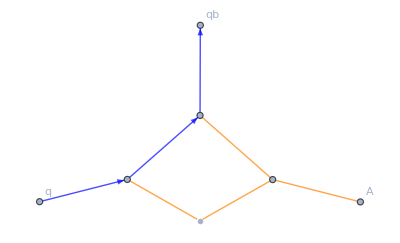
{1,-Graphics-}

```mathematica
PlotSuperindexDiagram[
DiagramsAqbqReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->False
]
```

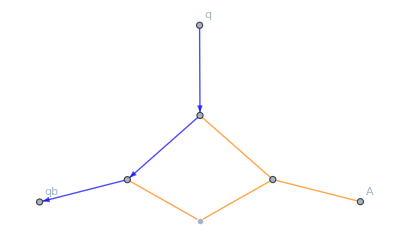
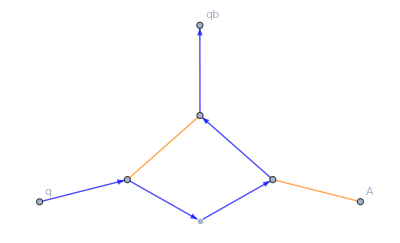
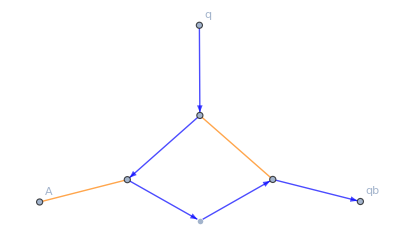
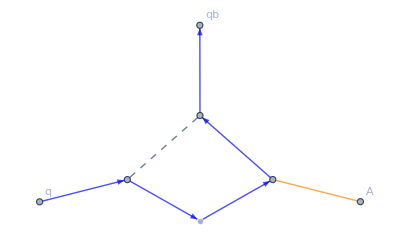
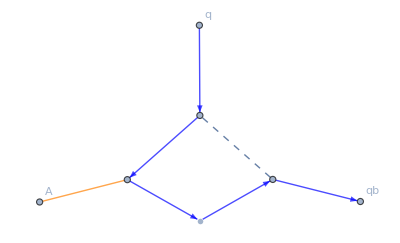
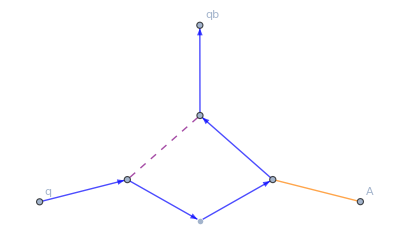
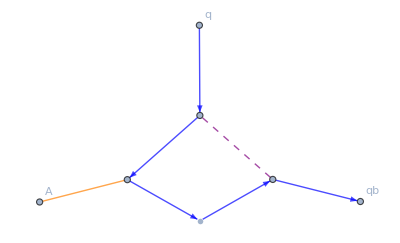
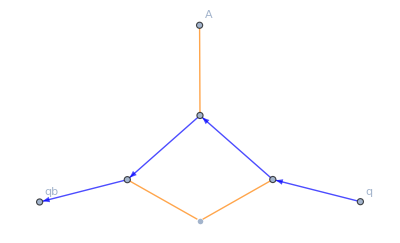
{{1,-Graphics-},{1,-Graphics-},{-1,-Graphics-},{-1,-Graphics-},{-1,-Graphics-},{-1,-Graphics-},{-1,-Graphics-},{-1,-Graphics-},{-1,-Graphics-},{1,-Graphics-},{-1,-Graphics-},{-1,-Graphics-}}

```mathematica
PlotSuperindexDiagram[
DiagramsAqbqReduced,SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple},c->Dotted},
"ShowEdgeLabels"->False
]
```

### Get Full diagrams and reroute the momenta for use in finite T setups

```mathematica
RerouteFermionicMomenta::usage
```

RerouteFermionicMomenta[diagrams, setup, derivativeList]

Reroute external fermionic momenta in diagrams such that Matsubara frequencies are automatically correctly routed.
If a closed fermion loop is present, the momentum in this loop is marked by attaching the character 'f' to it (i.e. q -> qf in such a loop).
The first argument to this function is a list of diagrams, the second one is the corresponding QMeS setup. The third argument is the derivative list that has been used to derive the set of diagrams.
Be aware, that the rerouting exploits momentum conservation - therefore, one of the external momenta may be eliminated if this is not yet the case.

```mathematica
DiagramsAqbqFull=SuperindexToFullDiagrams[DiagramsAqbqReduced,SetupfRGQCD,DerivativeListAqbq];
RerouteFermionicMomenta[DiagramsAqbqFull,SetupfRGQCD,DerivativeListAqbq]
```

{{GAA[{-q,v$51934,c$51934,q,v$51903,c$51903}] GAA[{q,v$51907,c$51907,-q,v$51900,c$51900}] GAA[{-p2-p3+q,v$51918,c$51918,p2+p3-q,v$51913,c$51913}] Gqqb[{p3-q,d$51925,c$51925,f$51925,-p3+q,d$51930,c$51930,f$51930}] RdotAA[{-q,v$51900,c$51900,q,v$51903,c$51903}] ΓAAA[{q,v$51907,c$51907,p2+p3-q,v$51913,c$51913,-p2-p3,v1,c1}] ΓAqbq[{-q,v$51934,c$51934,-p3+q,d$51930,c$51930,f$51930,p3,d3,c3,f3}] ΓAqbq[{-p2-p3+q,v$51918,c$51918,p2,d2,c2,f2,p3-q,d$51925,c$51925,f$51925}]},{GAA[{-q,v$52014,c$52014,q,v$51982,c$51982}] GAA[{q,v$51986,c$51986,-q,v$51979,c$51979}] GAA[{p2+p3+q,v$52008,c$52008,-p2-p3-q,v$52002,c$52002}] Gqqb[{-p2-q,d$51993,c$51993,f$51993,p2+q,d$51998,c$51998,f$51998}] RdotAA[{-q,v$51979,c$51979,q,v$51982,c$51982}] ΓAAA[{p2+p3+q,v$52008,c$52008,-q,v$52014,c$52014,-p2-p3,v1,c1}] ΓAqbq[{-p2-p3-q,v$52002,c$52002,p2+q,d$51998,c$51998,f$51998,p3,d3,c3,f3}] ΓAqbq[{q,v$51986,c$51986,p2,d2,c2,f2,-p2-q,d$51993,c$51993,f$51993}]},{-GAA[{p2+p3-q,v$52081,c$52081,-p2-p3+q,v$52088,c$52088}] Gqqb[{-p2+q,d$52061,c$52061,f$52061,p2-q,d$52093,c$52093,f$52093}] Gqqb[{-p2+q,d$52065,c$52065,f$52065,p2-q,d$52058,c$52058,f$52058}] Gqqb[{-2 p2-p3+q,d$52076,c$52076,f$52076,2 p2+p3-q,d$52071,c$52071,f$52071}] Rdotqbq[{p2-q,d$52058,c$52058,f$52058,-p2+q,d$52061,c$52061,f$52061}] ΓAqbq[{-p2-p3,v1,c1,2 p2+p3-q,d$52071,c$52071,f$52071,-p2+q,d$52065,c$52065,f$52065}] ΓAqbq[{p2+p3-q,v$52081,c$52081,p2,d2,c2,f2,-2 p2-p3+q,d$52076,c$52076,f$52076}] ΓAqbq[{-p2-p3+q,v$52088,c$52088,p2-q,d$52093,c$52093,f$52093,p3,d3,c3,f3}]},{-GAA[{-q,v$52149,c$52149,q,v$52156,c$52156}] Gqqb[{-p2+q,d$52140,c$52140,f$52140,p2-q,d$52172,c$52172,f$52172}] Gqqb[{-p2+q,d$52144,c$52144,f$52144,p2-q,d$52137,c$52137,f$52137}] Gqqb[{p3+q,d$52166,c$52166,f$52166,-p3-q,d$52161,c$52161,f$52161}] Rdotqbq[{p2-q,d$52137,c$52137,f$52137,-p2+q,d$52140,c$52140,f$52140}] ΓAqbq[{-p2-p3,v1,c1,p2-q,d$52172,c$52172,f$52172,p3+q,d$52166,c$52166,f$52166}] ΓAqbq[{-q,v$52149,c$52149,p2,d2,c2,f2,-p2+q,d$52144,c$52144,f$52144}] ΓAqbq[{q,v$52156,c$52156,-p3-q,d$52161,c$52161,f$52161,p3,d3,c3,f3}]},{-Gqqb[{-p2+q,d$52219,c$52219,f$52219,p2-q,d$52251,c$52251,f$52251}] Gqqb[{-p2+q,d$52223,c$52223,f$52223,p2-q,d$52216,c$52216,f$52216}] Gqqb[{-2 p2-p3+q,d$52234,c$52234,f$52234,2 p2+p3-q,d$52229,c$52229,f$52229}] GΠΠ[{p2+p3-q,a$52239,-p2-p3+q,a$52246}] Rdotqbq[{p2-q,d$52216,c$52216,f$52216,-p2+q,d$52219,c$52219,f$52219}] ΓAqbq[{-p2-p3,v1,c1,2 p2+p3-q,d$52229,c$52229,f$52229,-p2+q,d$52223,c$52223,f$52223}] ΓΠqbq[{p2+p3-q,a$52239,p2,d2,c2,f2,-2 p2-p3+q,d$52234,c$52234,f$52234}] ΓΠqbq[{-p2-p3+q,a$52246,p2-q,d$52251,c$52251,f$52251,p3,d3,c3,f3}]},{-Gqqb[{-p2+q,d$52298,c$52298,f$52298,p2-q,d$52330,c$52330,f$52330}] Gqqb[{-p2+q,d$52302,c$52302,f$52302,p2-q,d$52295,c$52295,f$52295}] Gqqb[{p3+q,d$52324,c$52324,f$52324,-p3-q,d$52319,c$52319,f$52319}] GΠΠ[{-q,a$52307,q,a$52314}] Rdotqbq[{p2-q,d$52295,c$52295,f$52295,-p2+q,d$52298,c$52298,f$52298}] ΓAqbq[{-p2-p3,v1,c1,p2-q,d$52330,c$52330,f$52330,p3+q,d$52324,c$52324,f$52324}] ΓΠqbq[{-q,a$52307,p2,d2,c2,f2,-p2+q,d$52302,c$52302,f$52302}] ΓΠqbq[{q,a$52314,-p3-q,d$52319,c$52319,f$52319,p3,d3,c3,f3}]},{-Gqqb[{-p2+q,d$52377,c$52377,f$52377,p2-q,d$52407,c$52407,f$52407}] Gqqb[{-p2+q,d$52381,c$52381,f$52381,p2-q,d$52374,c$52374,f$52374}] Gqqb[{-2 p2-p3+q,d$52392,c$52392,f$52392,2 p2+p3-q,d$52387,c$52387,f$52387}] Gσσ[{p2+p3-q,-p2-p3+q}] Rdotqbq[{p2-q,d$52374,c$52374,f$52374,-p2+q,d$52377,c$52377,f$52377}] ΓAqbq[{-p2-p3,v1,c1,2 p2+p3-q,d$52387,c$52387,f$52387,-p2+q,d$52381,c$52381,f$52381}] Γσqbq[{p2+p3-q,p2,d2,c2,f2,-2 p2-p3+q,d$52392,c$52392,f$52392}] Γσqbq[{-p2-p3+q,p2-q,d$52407,c$52407,f$52407,p3,d3,c3,f3}]},{-Gqqb[{-p2+q,d$52454,c$52454,f$52454,p2-q,d$52484,c$52484,f$52484}] Gqqb[{-p2+q,d$52458,c$52458,f$52458,p2-q,d$52451,c$52451,f$52451}] Gqqb[{p3+q,d$52478,c$52478,f$52478,-p3-q,d$52473,c$52473,f$52473}] Gσσ[{-q,q}] Rdotqbq[{p2-q,d$52451,c$52451,f$52451,-p2+q,d$52454,c$52454,f$52454}] ΓAqbq[{-p2-p3,v1,c1,p2-q,d$52484,c$52484,f$52484,p3+q,d$52478,c$52478,f$52478}] Γσqbq[{-q,p2,d2,c2,f2,-p2+q,d$52458,c$52458,f$52458}] Γσqbq[{q,-p3-q,d$52473,c$52473,f$52473,p3,d3,c3,f3}]},{-GAA[{-q,v$52562,c$52562,q,v$52531,c$52531}] GAA[{q,v$52535,c$52535,-q,v$52528,c$52528}] Gqqb[{-p2-q,d$52542,c$52542,f$52542,p2+q,d$52547,c$52547,f$52547}] Gqqb[{p3-q,d$52553,c$52553,f$52553,-p3+q,d$52558,c$52558,f$52558}] RdotAA[{-q,v$52528,c$52528,q,v$52531,c$52531}] ΓAqbq[{-p2-p3,v1,c1,p2+q,d$52547,c$52547,f$52547,p3-q,d$52553,c$52553,f$52553}] ΓAqbq[{-q,v$52562,c$52562,-p3+q,d$52558,c$52558,f$52558,p3,d3,c3,f3}] ΓAqbq[{q,v$52535,c$52535,p2,d2,c2,f2,-p2-q,d$52542,c$52542,f$52542}]},{GAA[{p2+p3-q,v$52631,c$52631,-p2-p3+q,v$52637,c$52637}] GAA[{-q,v$52619,c$52619,q,v$52626,c$52626}] Gqqb[{-p2+q,d$52610,c$52610,f$52610,p2-q,d$52642,c$52642,f$52642}] Gqqb[{-p2+q,d$52614,c$52614,f$52614,p2-q,d$52607,c$52607,f$52607}] Rdotqbq[{p2-q,d$52607,c$52607,f$52607,-p2+q,d$52610,c$52610,f$52610}] ΓAAA[{q,v$52626,c$52626,p2+p3-q,v$52631,c$52631,-p2-p3,v1,c1}] ΓAqbq[{-q,v$52619,c$52619,p2,d2,c2,f2,-p2+q,d$52614,c$52614,f$52614}] ΓAqbq[{-p2-p3+q,v$52637,c$52637,p2-q,d$52642,c$52642,f$52642,p3,d3,c3,f3}]},{-Gqqb[{-p2-q,d$52700,c$52700,f$52700,p2+q,d$52705,c$52705,f$52705}] Gqqb[{p3-q,d$52711,c$52711,f$52711,-p3+q,d$52716,c$52716,f$52716}] GΠΠ[{-q,a$52720,q,a$52689}] GΠΠ[{q,a$52693,-q,a$52686}] RdotΠΠ[{-q,a$52686,q,a$52689}] ΓAqbq[{-p2-p3,v1,c1,p2+q,d$52705,c$52705,f$52705,p3-q,d$52711,c$52711,f$52711}] ΓΠqbq[{-q,a$52720,-p3+q,d$52716,c$52716,f$52716,p3,d3,c3,f3}] ΓΠqbq[{q,a$52693,p2,d2,c2,f2,-p2-q,d$52700,c$52700,f$52700}]},{-Gqqb[{-p2-q,d$52776,c$52776,f$52776,p2+q,d$52781,c$52781,f$52781}] Gqqb[{p3-q,d$52787,c$52787,f$52787,-p3+q,d$52792,c$52792,f$52792}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓAqbq[{-p2-p3,v1,c1,p2+q,d$52781,c$52781,f$52781,p3-q,d$52787,c$52787,f$52787}] Γσqbq[{-q,-p3+q,d$52792,c$52792,f$52792,p3,d3,c3,f3}] Γσqbq[{q,p2,d2,c2,f2,-p2-q,d$52776,c$52776,f$52776}]}}